```mathematica
data = Import[FileNameJoin[{NotebookDirectory[],"data.txt"}],"Table"];
```

NotebookDirectory::nosv: The notebook 6c4d1c34-ec47-473e-8475-787ec66f8929 is not saved.

Import::chtype: First argument FileNameJoin[{$Failed,data.txt}] is not a valid file, directory, or URL specification.

```mathematica
SingDir = data[[All,{1,6}]];
SingInv = data[[All,{1,7}]];
DoubDir = data[[All,{1,8}]];
DoubInv = data[[All,{1,9}]];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
ListPlot[{SingDir, SingInv}, PlotRange->Automatic, PlotLegends->{"diretta","inversa"}]
```

-Graphics-

```mathematica
ListPlot[{DoubDir, DoubInv}, PlotRange->Automatic, PlotLegends->{"diretta","inversa"}]
```

-Graphics-

```mathematica
Solve[(n+1)^2/ n^2 == 2^53,n]
```

{{n→(1-67108864 √2)/9007199254740991},{n→(1+67108864 √2)/9007199254740991}}

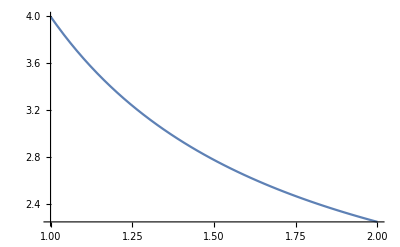

```mathematica
Plot[(x+1)^2 / x^2,{x, 1,2}]
```